```mathematica
<<CustomTicks`
```

```mathematica
tickll=LogTicks[-10,10];
Do[tickll[[i,1]]=10^tickll[[i,1]],{i,1,Length[tickll]}];
tickll;
```

#### projections from this work

```mathematica
ma={200,300,500,1000,2000,3000,4000,5000,6000,7000,8000,9000};
(*fa={485,622,858,1156,1133,1219,1137,1078,620,720,491,544};*)
(*mucfa={1823,4917,8754,14306,15567,14827,12590,9269,5881,3021,1167,296};*)
mucfa={257,327,427,640,695,685,620,507,403,292,197,107};
(*mucvbffa={208,287,369,550,625,633,575,472,378,279,190,106};*)
mucdata=Table[{ma[[i]],mucfa[[i]]},{i,1,Length[ma]}];
(*mucvbfdata=Table[{ma[[i]],mucvbffa[[i]]},{i,1,Length[ma]}];*)
ma3TeV={200,300,500,800,1000,1200,1500,1800,2000,2200,2500,2700,2900};
muc3TeVfa={131,170,188,192,183,170,141,113,94,74,50,31,18};
(*muc3TeVvbffa={110,135,166,177,171,161,135,109,92,73,49,31,18};*)
muc3TeVdata=Table[{ma3TeV[[i]],muc3TeVfa[[i]]},{i,1,Length[ma3TeV]}];
(*muc3TeVvbfdata=Table[{ma3TeV[[i]],muc3TeVvbffa[[i]]},{i,1,Length[ma3TeV]}];*)
```

## MuC projection

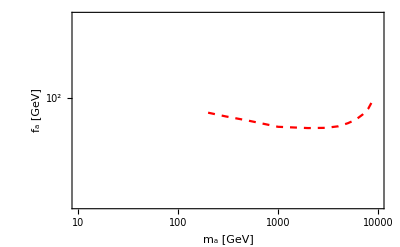

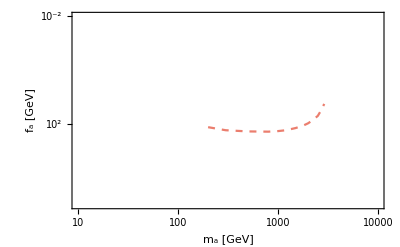

```mathematica
mucplot=ListLogLogPlot[mucdata,ScalingFunctions->{Identity,"Reverse"},Joined->True,PlotRange->{{10^1,10^4},{5*10^-1,10^5}},PlotStyle->{Red,Dashed,Thickness[0.004]},Frame->True,FrameTicks->{{tickll,Automatic},{tickll,Automatic}},FrameTicksStyle->Directive[Black,15,FontFamily->"Times"],FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a [GeV]",Black,15,FontFamily->"Times"]}(*,PlotLabel->Style["Standard axion benchmark",Black,18,FontFamily->"Times"]*)]
(*mucvbfplot=ListLogLogPlot[mucvbfdata,ScalingFunctions->{Identity,"Reverse"},Joined->True,PlotRange->{{10^1,10^4},{10^-2,10^5}},PlotStyle->{RGBColor[21/256,112/256,21/256,1],Dashed,Thickness[0.004]},Frame->True,FrameTicks->{{tickll,Automatic},{tickll,Automatic}},FrameTicksStyle->Directive[Black,15,FontFamily->"Times"],FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a [GeV]",Black,15,FontFamily->"Times"]}]*)
muc3TeVplot=ListLogLogPlot[muc3TeVdata,ScalingFunctions->{Identity,"Reverse"},Joined->True,PlotRange->{{10^1,10^4},{10^-2,10^5}},PlotStyle->{ColorData[24][1],Dashed,Thickness[0.004]},Frame->True,FrameTicks->{{tickll,Automatic},{tickll,Automatic}},FrameTicksStyle->Directive[Black,15,FontFamily->"Times"],FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a [GeV]",Black,15,FontFamily->"Times"]}(*,PlotLabel->Style["Standard axion benchmark",Black,18,FontFamily->"Times"]*)]
(*muc3TeVvbfplot=ListLogLogPlot[muc3TeVvbfdata,ScalingFunctions->{Identity,"Reverse"},Joined->True,PlotRange->{{10^1,10^4},{10^-2,10^5}},PlotStyle->{RGBColor[0.574,0.738,0.574,0.8],Dashed,Thickness[0.004]},Frame->True,FrameTicks->{{tickll,Automatic},{tickll,Automatic}},FrameTicksStyle->Directive[Black,15,FontFamily->"Times"],FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a [GeV]",Black,15,FontFamily->"Times"]}]*)
```

## Input data from other experiment constraints

```mathematica
SetDirectory["/Users/soubhik/Library/Mobile Documents/com~apple~CloudDocs/Documents/Projects/alp_muc"]
```

/Users/soubhik/Library/Mobile Documents/com~apple~CloudDocs/Documents/Projects/alp_muc

```mathematica
LHCdrellyanold=Import["E:\\李沛然\\课程\\物理\\Particle research\\axion_MuC\\plot\\constraints\\LHC_drellyan.csv","CSV"];(*photon fusion,require proton in final state*)
(*LHCdrellyanold2=Import["E:\\李沛然\\课程\\物理\\Particle research\\axion_MuC\\plot\\constraints\\LHC_drellyan_2.csv","CSV"];*)

(*LHCH2gammagammaold=Import["E:\\李沛然\\课程\\物理\\Particle research\\axion_MuC\\plot\\constraints\\LHC_H2gammagamma.csv","CSV"];*)
LHCPbPbold=Import["E:\\李沛然\\课程\\物理\\Particle research\\axion_MuC\\plot\\constraints\\LHC_PbPb.csv","CSV"];
LHCggF=Import["E:\\李沛然\\课程\\物理\\Particle research\\axion_MuC\\plot\\constraints\\LHC_ggF.csv","CSV"];
LHC95gammagamma=Import["E:\\李沛然\\课程\\物理\\Particle research\\axion_MuC\\plot\\constraints\\LHC_95GeVdiphoton.csv","CSV"];
LEP=Import["E:\\李沛然\\课程\\物理\\Particle research\\axion_MuC\\plot\\constraints\\LEP.csv","CSV"];
LHClowmassdiphoton=Import["E:\\李沛然\\课程\\物理\\Particle research\\axion_MuC\\plot\\constraints\\LHC_v1_lowmassdiphoton.csv","CSV"];
LHC10to70diphoton=Import["E:\\李沛然\\课程\\物理\\Particle research\\axion_MuC\\plot\\constraints\\LHC_10to70GeV.csv","CSV"];
```

```mathematica
LHCdrellyandata=Table[{LHCdrellyanold[[i]][[1]],1/LHCdrellyanold[[i]][[2]]*Sqrt[2.2*10^-3]/(128*Pi)*1000(*TeV2GeV*)},{i,1,Length[LHCdrellyanold]}];(*photon fusion,require proton in final state*)
(*LHCH2gammagammadata=Table[{LHCH2gammagammaold[[i]][[1]],1/LHCH2gammagammaold[[i]][[2]]*Sqrt[2.2*10^-3*418000]/(128*Pi)*1000(*TeV2GeV,418000 is the vbf ratio for gluon and photon*)},{i,1,Length[LHCH2gammagammaold]}];*)
LHCPbPbdata=Table[{LHCPbPbold[[i]][[1]],1/LHCPbPbold[[i]][[2]]*Sqrt[2.2*10^-3]/(128*Pi)*1000(*TeV2GeV*)},{i,1,Length[LHCPbPbold]}];
LHCggFdata=Table[{LHCggF[[i]][[1]],1/LHCggF[[i]][[2]]*0.0168/(2*Pi)*2(*Subscript[c, γ]=2*)},{i,1,Length[LHCggF]}];
gg2axxs={5.46,5.36,5.14,4.87,4.6,4.38,4.19,4.06,3.93,3.83,3.69,3.59,3.5,3.39,3.32,3.25,3.21,3.16,3.06,3.0,2.95,2.91,2.86,2.83,2.79,2.75,2.72,2.7,2.62,2.6,2.55};(*madgraph generated pp2ax*)
LHC95gammagammadata=Table[{LHC95gammagamma[[i]][[1]],Sqrt[(gg2axxs[[i]]*2.2*10^-3)/(LHC95gammagamma[[i]][[2]]*10^-3(*fb2pb*))]*1000},{i,1,Length[LHC95gammagamma]}];
LEPdata=Table[{LEP[[i]][[1]],1/LEP[[i]][[2]]*0.0168/(2*Pi)*2(*Subscript[c, γ]=2*)*Sqrt[2.2*10^-3]},{i,1,Length[LEP]}];
LHClowmassdiphotondata=Table[{LHClowmassdiphoton[[i]][[1]],LHClowmassdiphoton[[i]][[2]]*0.1(*c=10->1*)*(1+1)/(1+5/3)(*Subscript[c, 1]=5/3->1*)},{i,1,Length[LHClowmassdiphoton]}];
LHC10to70diphotondata=Table[{LHC10to70diphoton[[i]][[1]],LHC10to70diphoton[[i]][[2]]*0.1(*c=10->1*)*1000(*TeVtoGeV*)*1/2(*1/4pi to 1/8pi*)*(1+1)/(1+5/3)(*Subscript[c, 1]=5/3->1*)},{i,1,Length[LHC10to70diphoton]}];
```

## Plot other experiment constraints

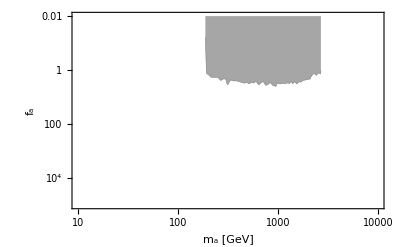

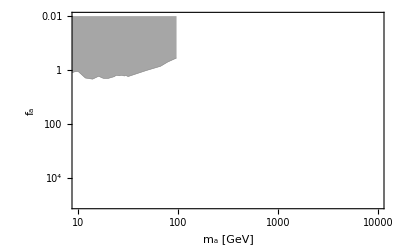

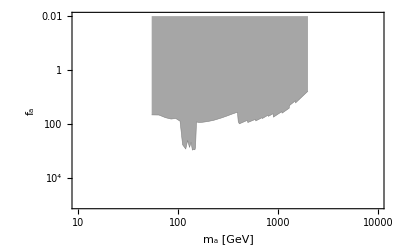

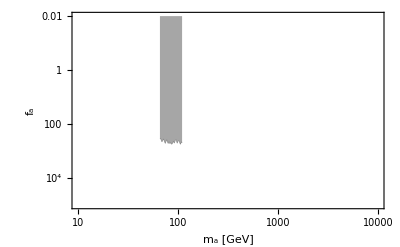

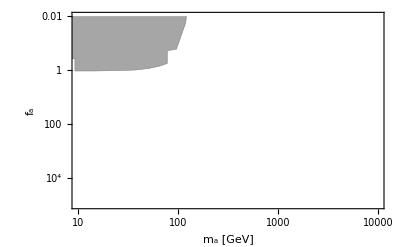

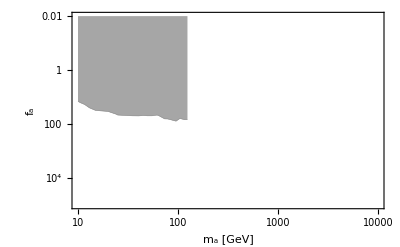

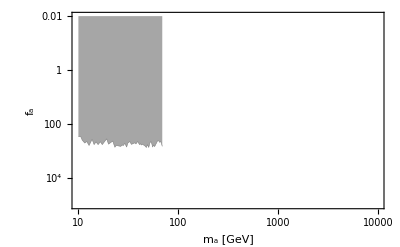

```mathematica
LHCdrellyanplot=ListLogLogPlot[LHCdrellyandata,ScalingFunctions->{Identity,"Reverse"},Joined->True,PlotRange->{{10^1,10^4},{10^-2,10^5}},Filling->Top,FillingStyle->Directive[Opacity[0.7],(*ColorData[24][6]*)Gray],PlotStyle->{(*ColorData[24][6]*)Gray,Thickness[0.001]},Frame->True,FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a",Black,15,FontFamily->"Times"]}]
LHCPbPbplot=ListLogLogPlot[LHCPbPbdata,ScalingFunctions->{Identity,"Reverse"},Joined->True,PlotRange->{{10^1,10^4},{10^-2,10^5}},Filling->Top,FillingStyle->Directive[Opacity[0.7],(*Cyan*)Gray],PlotStyle->{(*Cyan*)Gray,Thickness[0.001]},Frame->True,FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a",Black,15,FontFamily->"Times"]}]
LHCggFplot=ListLogLogPlot[LHCggFdata,ScalingFunctions->{Identity,"Reverse"},Joined->True,PlotRange->{{10^1,10^4},{10^-2,10^5}},Filling->Top,FillingStyle->Directive[Opacity[0.7],(*ColorData[24][3]*)Gray],PlotStyle->{(*ColorData[24][3]*)Gray,Thickness[0.001]},Frame->True,FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a",Black,15,FontFamily->"Times"]}]
LHC95gammagammaplot=ListLogLogPlot[LHC95gammagammadata,ScalingFunctions->{Identity,"Reverse"},Joined->True,PlotRange->{{10^1,10^4},{10^-2,10^5}},Filling->Top,FillingStyle->Directive[Opacity[0.7],(*ColorData[24][4]*)Gray],PlotStyle->{(*ColorData[24][4]*)Gray,Thickness[0.001]},Frame->True,FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a",Black,15,FontFamily->"Times"]}]
LEPplot=ListLogLogPlot[LEPdata,ScalingFunctions->{Identity,"Reverse"},Joined->True,PlotRange->{{10^1,10^4},{10^-2,10^5}},Filling->Top,FillingStyle->Directive[Opacity[0.7],(*ColorData[24][2]*)Gray],PlotStyle->{(*ColorData[24][2]*)Gray,Thickness[0.001]},Frame->True,FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a",Black,15,FontFamily->"Times"]}]
LHClowmassdiphotonplot=ListLogLogPlot[LHClowmassdiphotondata,ScalingFunctions->{Identity,"Reverse"},Joined->True,PlotRange->{{10^1,10^4},{10^-2,10^5}},Filling->Top,FillingStyle->Directive[Opacity[0.7],(*ColorData[24][1]*)Gray],PlotStyle->{(*ColorData[24][1]*)Gray,Thickness[0.001]},Frame->True,FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a",Black,15,FontFamily->"Times"]}]
LHC10to70diphotonplot=ListLogLogPlot[LHC10to70diphotondata,ScalingFunctions->{Identity,"Reverse"},Joined->True,PlotRange->{{10^1,10^4},{10^-2,10^5}},Filling->Top,FillingStyle->Directive[Opacity[0.7],Gray],PlotStyle->{Gray,Thickness[0.001]},Frame->True,FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a",Black,15,FontFamily->"Times"]}]
```

## Plot theory constraints

### EFT

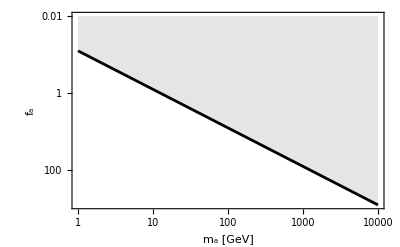

```mathematica
faEFT[ma_]:=ma/(4Pi);(*EFT consistency, EFT breaks down when ma > 4 Pi fa*)
EFTConsPlot=LogLogPlot[faEFT[ma],{ma,1,10^4},ScalingFunctions->{Identity,"Reverse"},PlotRange->{{10^1,10^4},{10^-2,10^5}},PlotStyle->{Black,Thickness[0.005]},Frame->True,Filling->Top,FillingStyle->Opacity[0.1],FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a",Black,15,FontFamily->"Times"]}]
```

### Product Group

```mathematica
v=246.22;
yi[mi_]:=mi Sqrt[2]/v;
yu=yi[mu]/.{mu->2.16*10^-3};
yd=yi[md]/.{md->4.70*10^-3};
ys=yi[ms]/.{ms->93.5*10^-3};
yc=yi[mc]/.{mc->1.273};
yb=yi[mb]/.{mb->4.183};
yt=yi[mt]/.{mt->172.4};

K1=0.466;K2=1.678;alphaHalf=0.146;
C3[nS_,nF_]:=K1/2 Exp[-3K2]Exp[-(nS-2nF)alphaHalf];
y1=1;y2=1;
b[S_,F_]:=11-S/6-2F/3;
nS1=3;nF1=8;b1=b[nS1,nF1];
nS2=6;nF2=2;b2=b[nS2,nF2];
nS3=3;nF3=2;b3=b[nS3,nF3];
Kfac = 40/9(yu yd ys yc yb yt)/(4Pi)^6;
bQCD=7;
mz=91.1880;
alphamz=0.1180;
alphaQCD[M_]:=1/(1/alphamz+bQCD/(2Pi)Log[M/mz]);
```

```mathematica
ProdGrpFinal={{10^13,0.134},{10^12,0.152},{10^11,0.177},{10^10,0.212},{10^9,0.265}};(*{M,alpha1M} tuples, for these values ma1 and ma2 have approximately the same mass, while ma3 is a bit heavier*)
faProdGrp[ma_,alpha1M_,M_]:=1/ma Sqrt[Kfac C3[nS1,nF1](y1 y2)/(12 Pi^2)((2Pi)/alpha1M)^6 M^4(1/(2Pi))^(b1-4)Gamma[b1/2-2]Exp[-2Pi/alpha1M]];(*this is only valid for ma1, to be used for plotting*)
```

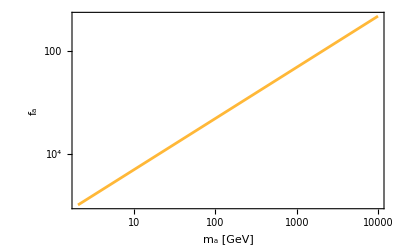

```mathematica
ProdGrpPlot=LogLogPlot[faProdGrp[ma,ProdGrpFinal[[3]][[2]],ProdGrpFinal[[3]][[1]]],{ma,1,10^4},ScalingFunctions->{Identity,"Reverse"},PlotRange->{{10^1,10^4},{10^-2,10^5}},PlotStyle->{ColorData[24][2],Thickness[0.005]},Frame->True,FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a",Black,15,FontFamily->"Times"]}]
```

### Mirror Model

1645.19

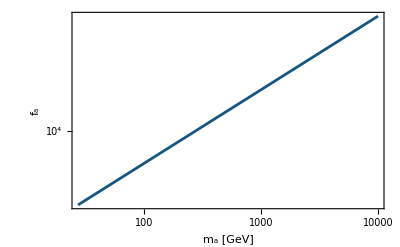

```mathematica
LamPrime=1645.19(*This is the mirror confinement scale for vprime = 10^14 GeV*)
faMirrMod[ma_]:=LamPrime^2/ma;
MirrModPlot=LogLogPlot[faMirrMod[ma],{ma,1,10^4},ScalingFunctions->{Identity,"Reverse"},PlotRange->{{10^1,10^4},{10^-2,10^5}},PlotStyle->{ColorData[24][7],Thickness[0.005]},Frame->True,FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a",Black,15,FontFamily->"Times"]}]
```

### Extra Dim Bulk Gauge Field Model (Don’t use!)

```mathematica
mPi=135/1000;
fPi=92/1000;
fa[R_]:=1/(Pi Sqrt[4Pi alphaQCD[1/R]] R);
```

```mathematica
fa[R]/.{R->10^-4}
```

3324.53

```mathematica
faVals=Table[10^n,{n,-2,5,0.1}];
RVals={};
For[i=1,i<Length[faVals]+1,i++,AppendTo[RVals,NSolve[fa[R]==faVals[[i]],R,Reals][[1]][[1]][[2]]]](*there is a one-to-one relation between fa and R*)
mAxExtraDim[eps_,R_]:=Sqrt[2 Kfac C3[0,0]](*Sqrt[Exp[6*0.292]]*)((2Pi)/alphaQCD[1/R])^3 1/(fa[R] R^2)Exp[-Pi/alphaQCD[1/R](1-3 eps)]((6Pi eps)/alphaQCD[1/R])^(1/2(3-bQCD));
maVals={};
epsInput=0.5;
For[i=1,i<Length[RVals]+1,i++,AppendTo[maVals,mAxExtraDim[epsInput,RVals[[i]]]]]
```

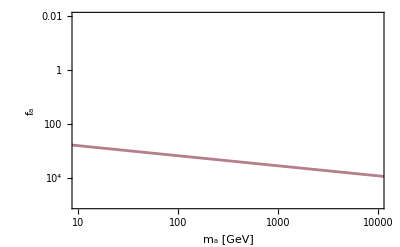

```mathematica
EDBulkGaugePlot=ListLogLogPlot[Transpose@{maVals,faVals},ScalingFunctions->{Identity,"Reverse"},Joined->True,PlotRange->{{10^1,10^4},{10^-2,10^5}},PlotStyle->{ColorData[24][8],Thickness[0.005]},Frame->True,FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a",Black,15,FontFamily->"Times"]}]
```

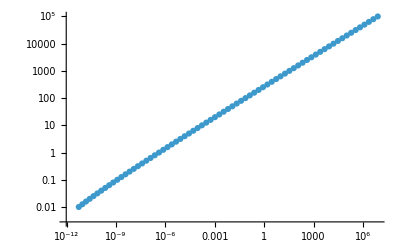

```mathematica
ListLogLogPlot[Transpose@{maVals,faVals}]
```

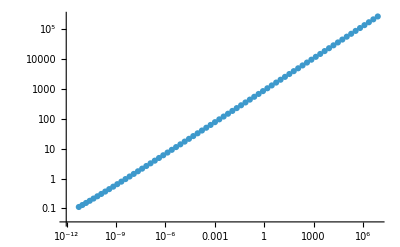

```mathematica
ListLogLogPlot[Transpose@{maVals,1/RVals}]
```

### PQ Quality Problem

```mathematica
Mpl=2.4*10^18;
faQuality[ma_,n_]:=(ma^(2/(n-2))10^(-10/(n-2)))/Mpl^((4-n)/(n-2));
```

```mathematica
faQuality[1,5]
```

621.447

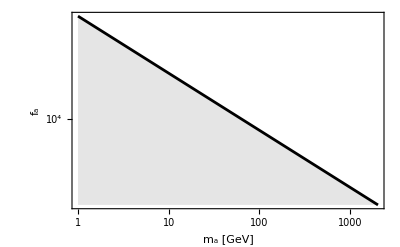

```mathematica
QProbPlot=LogLogPlot[faQuality[ma,5],{ma,1,10^4},ScalingFunctions->{Identity,"Reverse"},PlotRange->{{10^1,10^4},{10^-2,10^5}},PlotStyle->{Black,Thickness[0.005]},Frame->True,Filling->Bottom,FillingStyle->Opacity[0.1],FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a",Black,15,FontFamily->"Times"]}]
```

## Final Plot

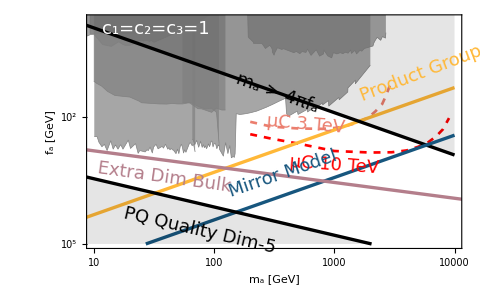

```mathematica
Show[mucplot,(*mucvbfplot,*)muc3TeVplot,(*muc3TeVvbfplot,*)LHCggFplot,LHClowmassdiphotonplot,LHC10to70diphotonplot,LHC95gammagammaplot,(*LHCH2gammagammaplot,*)LHCPbPbplot,LEPplot,LHCdrellyanplot,ProdGrpPlot,EFTConsPlot,MirrModPlot,EDBulkGaugePlot,QProbPlot,Epilog->{Text[Style["c_1=c_2=c_3=1",White,18,FontFamily->"Times"],Scaled[{0.04,0.94}],Left,{1,0}],Text[Style[Rotate["μC 3 TeV",-5 Degree],ColorData[24][1],18,FontFamily->"Times"],Scaled[{0.48,0.545}],Left,{1,0}],Text[Style[Rotate["μC 10 TeV",-4 Degree],Red,18,FontFamily->"Times"],Scaled[{0.54,0.37}],Left,{1,0}],Text[Style[Rotate["Mirror Model",19 Degree],ColorData[24][7],18,FontFamily->"Times"],Scaled[{0.38,0.24}],Left,{1,0}],Text[Style[Rotate["Product Group",21 Degree],ColorData[24][2],18,FontFamily->"Times"],Scaled[{0.73,0.65}],Left,{1,0}],Text[Style[Rotate["Extra Dim Bulk",-8 Degree],ColorData[24][8],18,FontFamily->"Times"],Scaled[{0.03,0.345}],Left,{1,0}],Text[Style[Rotate["m_a > 4πf_a",-20 Degree],Black,18,FontFamily->"Times"],Scaled[{0.4,0.728}],Left,{1,0}],Text[Style[Rotate["PQ Quality Dim-5",-13 Degree],Black,18,FontFamily->"Times"],Scaled[{0.1,0.15}],Left,{1,0}](*,Text[Style["w.o. VBS 3 TeV",RGBColor[0.574,0.738,0.574,0.8],13,FontFamily->"Times"],Scaled[{0.75,0.46}],Right,{1,0}]*)(*,Text[Style["w.o. VBS 10 TeV",RGBColor[21/256,112/256,21/256,1],13,FontFamily->"Times"],Scaled[{0.94,0.26}],Right,{1,0}]*)}]
```

```mathematica
Export["/Users/soubhik/Library/Mobile Documents/com~apple~CloudDocs/Documents/Projects/alp_muc/final_plot.pdf",%295,"PDF"]
```

/Users/soubhik/Library/Mobile Documents/com~apple~CloudDocs/Documents/Projects/alp_muc/final_plot.pdf